```mathematica
Clear["Global`*"]

(*---Matter-dominated perturbation equation---*)
n=-2/3;
δ=f[x]*x^n;
δDot=D[δ,x]*k;
δDotDot=D[δDot,x]*k;
perturbationEqn=δDotDot+4/(3 t) δDot==2/(3 t^2) (1-(cs^2 k^2)/(4 π G Subscript[ρ,0] a^2)) δ/. t->x/k/. Subscript[ρ,0]->(3 H0^2)/(8 π G a^3);
FofX=DSolve[perturbationEqn,f[x],x][[1,1,2]];
δofX=FullSimplify[FofX*x^n];
δofKA=δofX/. x->((2 k a^(3/2))/(3 H0));

(*---Hubble parameter and gravitational potential---*)
H[a_]:=H0 Sqrt[Ωm/a^3];
Ψ[a_]:=-(3 H0^2 Ωm)/(2 a^3);

(*---Solve perturbation equation---*)
ceff2[a_]:=0;
negligibleSolution=DSolve[a^2 H[a]^2 Δa''[a]+(3 a H[a]^2+a^2 H[a] H'[a]) Δa'[a]+(k^2 ceff2[a]^2/a^2+Ψ[a]) Δa[a]==0,Δa,a]//FullSimplify;
ceff2[a_]:=cs^2;
perturbedSolution=DSolve[a^2 H[a]^2 Δa''[a]+(3 a H[a]^2+a^2 H[a] H'[a]) Δa'[a]+(k^2 ceff2[a]^2/a^2+Ψ[a]) Δa[a]==0,Δa,a]//FullSimplify;
negligibleFunc=negligibleSolution[[1,1,2]];
perturbedFunc=Function[{a},(3/2)^((H0+Sqrt[25 H0^2-16 a cs^2 k^2])/(6 H0)) ((a^(3/2) k)/H0)^(-((H0+Sqrt[25 H0^2-16 a cs^2 k^2])/(6 H0))) C[1]+(2/3)^(Sqrt[25 H0^2-16 a cs^2 k^2]/(3 H0)-(H0+Sqrt[25 H0^2-16 a cs^2 k^2])/(6 H0)) ((a^(3/2) k)/H0)^(Sqrt[25 H0^2-16 a cs^2 k^2]/(3 H0)-(H0+Sqrt[25 H0^2-16 a cs^2 k^2])/(6 H0)) C[2]];

(*---Matching functions and derivatives at the start and end of the "kick"---*)
solutionsForConstants1=Solve[{ai CC==perturbedFunc[ai],CC==D[perturbedFunc[a],a]/. a->ai},{C[1],C[2]}]//FullSimplify;
startKick=perturbedFunc/. {C[1]->solutionsForConstants1[[1,1,2]],C[2]->solutionsForConstants1[[1,2,2]]};
solutionsForConstants2=Solve[{(negligibleFunc[af])==(startKick[af]),(D[negligibleFunc[a],a]/. a->af)==(D[startKick[a],a]/. a->af)},{C[1],C[2]}]//Simplify;
endKick=negligibleFunc/. {C[1]->solutionsForConstants2[[1,1,2]],C[2]->solutionsForConstants2[[1,2,2]]};

(*---Piecewise perturbation solution---*)
δgdm[a_]:=Piecewise[{{CC a,a<ai},{startKick[a],ai<=a<=af}},endKick[a]];

(*---Gravitational potential via the Poisson equation substitution---*)
phi[a_]:=-(3/2)*a*H[a]^2/k^2*δgdm[a];
phiExpr=Simplify[phi[a],Assumptions->{a>0,k>0,H0>0,Ωm>0}];
phiExpr // TraditionalForm
```

-1/(2 a^2 k^2)3 H0^2 Ωm (Piecewise[{{a CC, a<ai}, {1/(75 H0^2-16 ai cs^2 k^2 log((ai^(3/2) k)/H0)+16 ai cs^2 k^2 (-3+log(3/2)))2^(-(6 H0+√(25 H0^2-16 a cs^2 k^2)+√(25 H0^2-16 ai cs^2 k^2))/(6 H0)) 3^(-(√(25 H0^2-16 a cs^2 k^2)+√(25 H0^2-16 ai cs^2 k^2))/(6 H0)) ai CC ((a^(3/2) k)/H0)^(-(H0+√(25 H0^2-16 a cs^2 k^2))/(6 H0)) ((ai^(3/2) k)/H0)^((H0-√(25 H0^2-16 ai cs^2 k^2))/(6 H0)) (2^((√(25 H0^2-16 a cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) (75 H0^2+15 √(25 H0^2-16 ai cs^2 k^2) H0-16 ai cs^2 k^2 (log((2 ai^(3/2) k)/(3 H0))+3)) ((a^(3/2) k)/H0)^((√(25 H0^2-16 a cs^2 k^2))/(3 H0))+2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 a cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) (75 H0^2-15 √(25 H0^2-16 ai cs^2 k^2) H0-16 ai cs^2 k^2 (log((2 ai^(3/2) k)/(3 H0))+3))), ai≤a≤af}, {-((2^(-(12 H0+√(25 H0^2-16 af cs^2 k^2)+√(25 H0^2-16 ai cs^2 k^2))/(6 H0)) 3^(-(6 H0+√(25 H0^2-16 af cs^2 k^2)+√(25 H0^2-16 ai cs^2 k^2))/(6 H0)) ai CC ((af^(3/2) k)/H0)^(-(H0+√(25 H0^2-16 af cs^2 k^2))/(6 H0)) ((ai^(3/2) k)/H0)^((H0-√(25 H0^2-16 ai cs^2 k^2))/(6 H0)) (16 ai cs^2 ((75 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) H0^2+15 √(25 H0^2-16 af cs^2 k^2) (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))+2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) H0+16 af cs^2 k^2 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (-3+log(3/2))) a^(5/2)+af^(5/2) (-75 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) H0^2+15 √(25 H0^2-16 af cs^2 k^2) (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))+2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) H0-16 af cs^2 k^2 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (-3+log(3/2)))) log((2 ai^(3/2) k)/(3 H0)) k^2-16 af (af^(5/2)-a^(5/2)) cs^2 log((af^(3/2) k)/H0) (75 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) H0^2+15 √(25 H0^2-16 ai cs^2 k^2) (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))+2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) H0-48 ai cs^2 k^2 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)))-16 ai cs^2 k^2 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) log((2 ai^(3/2) k)/(3 H0))) k^2-3 ((1875 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) H0^4+375 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))+2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (√(25 H0^2-16 af cs^2 k^2)+√(25 H0^2-16 ai cs^2 k^2)) H0^3+25 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (-48 ai cs^2 k^2+16 af cs^2 (-3+log(3/2)) k^2+3 √(25 H0^2-16 af cs^2 k^2) √(25 H0^2-16 ai cs^2 k^2)) H0^2+80 cs^2 k^2 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))+2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (af √(25 H0^2-16 ai cs^2 k^2) (-3+log(3/2))-3 ai √(25 H0^2-16 af cs^2 k^2)) H0-256 af ai cs^4 k^4 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (-3+log(3/2))) a^(5/2)+af^(5/2) (-1875 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) H0^4+375 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))+2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (√(25 H0^2-16 af cs^2 k^2)-√(25 H0^2-16 ai cs^2 k^2)) H0^3+25 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (48 ai cs^2 k^2-16 af cs^2 (-3+log(3/2)) k^2+3 √(25 H0^2-16 af cs^2 k^2) √(25 H0^2-16 ai cs^2 k^2)) H0^2-16 cs^2 k^2 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))+2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (√(25 H0^2-16 ai cs^2 k^2) (-15+log(243/32)) af+15 ai √(25 H0^2-16 af cs^2 k^2)) H0+256 af ai cs^4 k^4 (2^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) ((af^(3/2) k)/H0)^((√(25 H0^2-16 af cs^2 k^2))/(3 H0))-2^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0)) 3^((√(25 H0^2-16 af cs^2 k^2))/(3 H0)) ((ai^(3/2) k)/H0)^((√(25 H0^2-16 ai cs^2 k^2))/(3 H0))) (-3+log(3/2))))))/(5 a^(3/2) af H0 √(25 H0^2-16 af cs^2 k^2) (75 H0^2-16 ai cs^2 k^2 log((ai^(3/2) k)/H0)+16 ai cs^2 k^2 (-3+log(3/2))))), True}}])

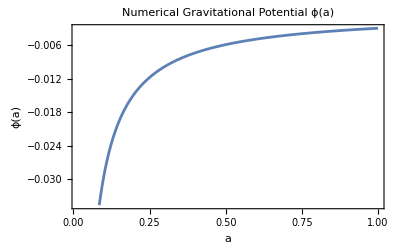

```mathematica
(*---Numerics---*)
h=0.7;
H0=0.0003335*h;
Ωm=1;
k=0.00528;
ai=0.01489;
af=0.02;
cs2want=0.0001;
da=Log[af/ai];
cs=Sqrt[cs2want/da];
CC=1;

(*---Numerical versions of the analytic functions---*)
deltaGDMNum[a_]:=δgdm[a]/. {H0->H0,Ωm->Ωm,k->k,ai->ai,af->af,cs->cs,CC->CC};
phiNum[a_]:=phi[a]/. {H0->H0,Ωm->Ωm,k->k,ai->ai,af->af,cs->cs,CC->CC};

(*---Plot the numerical gravitational potential---*)
Plot[phiNum[a],{a,ai,1},PlotLabel->"Numerical Gravitational Potential ϕ(a)",Frame->True,AxesLabel->{"a","ϕ(a)"}]
```

```mathematica
(*Fractional difference, log scale x-axis (recall absolute difference trick), superimpose vertical lines*)
(*Run through MD Python to cross-evaluate*)
(*Green's function solution--Wayne Hu, write solution as ∫Green (do it numerically, though)*)
(*Vary k from 10^-3 to 5*10^-2*)
```

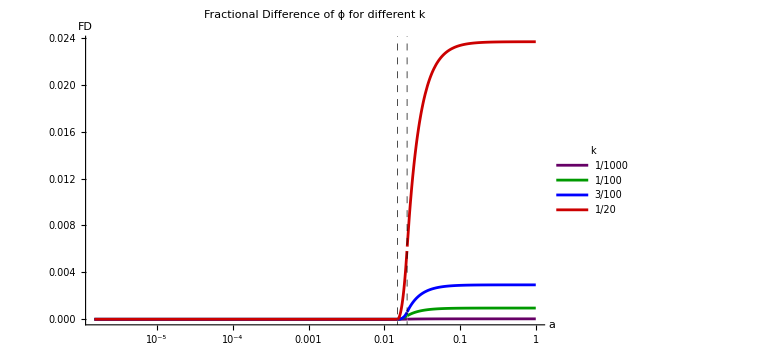

```mathematica
(*---Plot the fractional difference of gravitational potential---*)
phiRef[kVal_?NumericQ,a_]:=-(3/2)*a*H[a]^2/(kVal^2)*(CC*a); (**)
FDphi[kVal_?NumericQ,a_]:=Abs[(phiRef[kVal,a]-(phi[a]/. {k->kVal}))/phiRef[kVal,a]]; (**)
kVals={10^-3,10^-2,3*10^-2,5*10^-2};
colors={RGBColor[0.4,0,0.4],RGBColor[0,0.6,0],Blue,RGBColor[0.8,0,0]};

LogLinearPlot[
Evaluate[Table[FDphi[k,a],{k,kVals}]],{a,0.0001*ai,1},
PlotRange->All,
PlotStyle->colors,
AxesLabel->{"a","FD"},
PlotLegends->Placed[LineLegend[kVals,LegendLabel->"k"],{Left,Top}],
GridLines->{{ai,af},None},
GridLinesStyle->Directive[Black,Dashed,Thick],
PlotLabel->"Fractional Difference of ϕ for different k",
ImageSize->Large
]
(*Log Log plots, compare slopes, see additive factor of 2*)
```